```mathematica
ClearAll[Evaluate[Context[]<>"*"]];
ClearSystemCache[];
```

```mathematica
G2=Import[NotebookDirectory[]<>"points_G2_velocity.m"]//Interpolation;
G2gauss=Interpolation[Import[NotebookDirectory[]<>"brute_force_points_G2_velocity.m"]];
```

```mathematica
G2gausspts=Import[NotebookDirectory[]<>"brute_force_points_G2_velocity.m"];
```

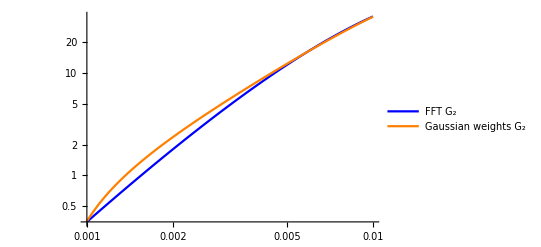

```mathematica
plot=LogLogPlot[{Re[G2[k]],Re[G2gauss[k]]},{k,0.001,0.01},PlotLegends->{"FFT G_2","Gaussian weights G_2"},PlotStyle->{Directive[Blue],Directive[Orange]}]
```

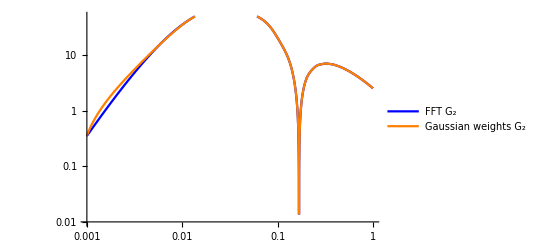

```mathematica
plot=LogLogPlot[{Re[G2[k]]//Abs,Re[G2gauss[k]]//Abs},{k,0.001,1},PlotLegends->{"FFT G_2","Gaussian weights G_2"},PlotStyle->{Directive[Blue],Directive[Orange]},PlotRange->{{0.001,1},{0.01,50}},PlotPoints->200]
```

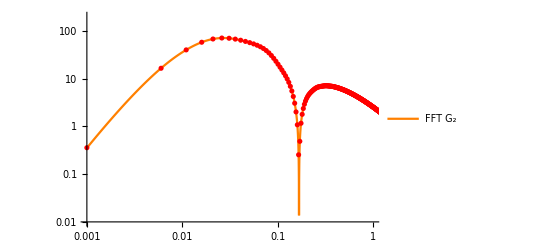

```mathematica
plot=Show[{LogLogPlot[{Re[G2[k]]//Abs},{k,0.001,1},PlotLegends->{"FFT G_2"},PlotStyle->{Directive[Blue],Directive[Orange]},PlotRange->{{0.001,1},{0.01,200}},PlotPoints->200],ListLogLogPlot[G2gausspts//Abs,PlotStyle->{Red}]}]
```

```mathematica
(* -> whatever. Clearly the FFT has the correct power-law behavior at low k!!! The issue is from interpolation... *)
```

```mathematica
Export[NotebookDirectory[]<>"comparison_plot_G2_velocity.pdf",plot];
```

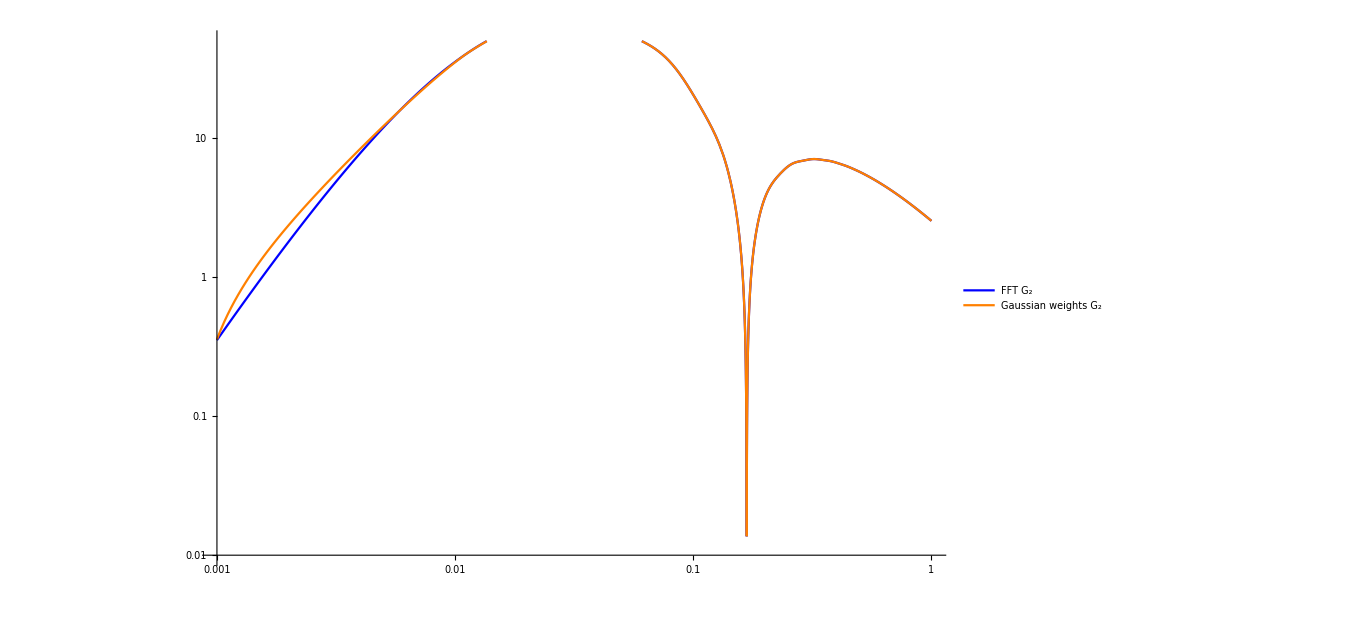

```mathematica
LogLogPlot[{Re[G2[k]]//Abs,Re[G2gauss[k]]//Abs},{k,0.001,1},PlotLegends->{"FFT G_2","Gaussian weights G_2"},PlotStyle->{Directive[Blue],Directive[Orange]},PlotRange->{{0.001,1},{0.01,50}},PlotPoints->200,ImageSize->1000]
```